#### Bouncing Ball Simulation

Let x[t] and y[t] be the position x and y of the ball in the instant t.

Model a surface as 2D curve that change in the x-direction:

```mathematica
surfx=Sin[x[t] Cos[2x[t]]];
```

```mathematica
surfEqs={surf[t]== surfx, gg[t]== D[surfx,x[t]]};
```

Move equations for the ball in terms of the velocity and the acceleration, as functions of the time:

```mathematica
moveEqs ={x'[t]== vx[t], vx'[t]==0, y'[t]==vy[t], vy'[t]== -gravity};
```

The velocity before a contact with the surface is the vector v1 with coordinates:

```mathematica
v1= {vx[t], vy[t]};
```

The contact point at the instant t:

```mathematica
contactPoint= {x[t] , surfx };
```

So, for the incident vector v1, use the surface orientation n, to return the reflection direction as v2=v1-2 Dot[n ,v1] n

Find the orientation of the surface:

```mathematica
g=D[contactPoint, x[t]]; (* The gradient of the surface*)
```

```mathematica
n= Normalize[Cross[g]]; (* The orientation of the surface *)
```

So the velocity after a contact with the surface is the vector v2:

```mathematica
v2= v1- 2 (n.v1) n;
```

The following rules define a event of bounce:

```mathematica
bounce=  WhenEvent[ y[t]<= surf[t]   , v1-> k v2];
```

Here k stands for a damping factor.

Now, run the simulation

Using:

```mathematica
bouncingBall= CreateSystemModel[Join[surfEqs,moveEqs, {bounce}],t][<| "InitialValues"-> {"x"-> 0.2, "y"->6.0}, "ParameterValues"-> {"gravity"-> 9.8, "k"-> 0.8}|>]
```

-Graphics-

Visualization of the simulation:

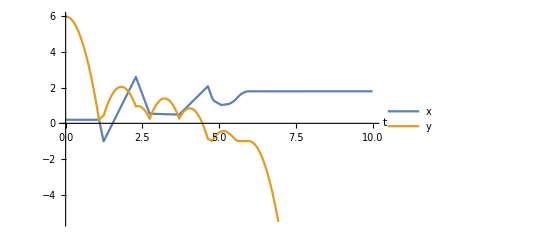

```mathematica
SystemModelPlot[{bouncingBall,10},{"x","y"}]
```

```mathematica
sim= SystemModelSimulate[bouncingBall, 10]
```

SystemModelSimulationData[…]

```mathematica
pts= Table[{x[t], surfx}/. x[t]-> m, {m,-4,4,0.1}];
```

```mathematica
data= Table[Graphics[{Disk[{sim["x"][t], sim["y"][t]},0.1],Line[pts]},PlotRange->{Automatic, {-2,6}}],{t,0,10,0.1}];
```

```mathematica
ListAnimate[data]
```

```mathematica
Export["result.mp4",%]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

result.mp4